## Maximum Bar Chart Height reader

## Data Generation

The code below was used to generate the dataset for the network shown in this notebook.

```mathematica
SeedRandom[1234]; 
randomList:=Table[{RandomInteger[{1,100}]*500,RandomWord[]},RandomInteger[{1,15}]];

dataset= ParallelTable[With[{j=CreateUUID[],rl=randomList},
	(Export[StringTemplate["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2\\``.jpg"][j],
	Rasterize[
	BarChart[Map[Labeled[#[[1]],#[[2]]]&,rl],
	ChartStyle->RandomChoice[ColorData["Charting"]], 
	ChartStyle->Thickness[RandomReal],
	Background->RandomColor[],(*this was only applied to 1/3 of the dataset*)
	ChartElementFunction->RandomChoice[ChartElementData["BarChart"]],
	BarSpacing->RandomChoice[{None,Automatic,Tiny,Small,Medium,Large}],
	PlotLabel->RandomChoice[WordList[]]
	],ImageSize->100]];
		Export[StringTemplate["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2\\``.mx"][j],
		rl[[All,1]]])],100000];
```

## Data Import for max bar height

Initial importing of image ids and data

```mathematica
(*location of the data files*)
dataDirectory="C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2\\";
(*names of all the different plots I generated*)
ids=Map[FileBaseName,Map[FileNameTake,FileNames[___~~".mx",dataDirectory]]];
(*exporting a mx file with all the names of the data files*)
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx",ids]
"C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx"
(*creating an mx file with the data that generated the jpg files used for training,
 associated with their name*)
mxs=AssociationMap[Import[FileNameJoin[{dataDirectory,StringJoin[#,".mx"]}]]&,ids];
(*exporting those files as well*)
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx",mxs]
```

Importing the ids after initialization

```mathematica
ids=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx"];
mxs=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx"];
```

Defining the data, training set, and test set

```mathematica
(*complete dataset*)
data=Flatten[Map[
	{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]
	->{Max[mxs[[Key[#]]]]}}&,ids]];
(*separate training and testing set (161 000 training, 3 913 testing*)
{training,testing}=TakeDrop[RandomSample[data],161000];
```

## VGG Net Modification to read max bar height

```mathematica
(*Importing vgg16Net as a base for my network*)
vgg16Net= NetModel["VGG-16 Trained on ImageNet Competition Data","UninitializedEvaluationNet"]
(*cutting off a few layers at the end to match the output form I want (one number)*)
vgg16Net2= NetReplacePart[NetTake[vgg16Net,{"conv1_1","pool5"}],
"Input"->NetEncoder[{"Image",100}]];
(*Adding a BatchNormalizationLayer before every ConvolutionLayer*)
vgg16Net3=NetInsert[vgg16Net2,"b1"->BatchNormalizationLayer[],"conv1_2"];
vgg16Net3=NetInsert[vgg16Net3,"b2"->BatchNormalizationLayer[],"conv2_1"];
vgg16Net3=NetInsert[vgg16Net3,"b3"->BatchNormalizationLayer[],"conv2_2"];
vgg16Net3=NetInsert[vgg16Net3,"b4"->BatchNormalizationLayer[],"conv3_1"];
vgg16Net3=NetInsert[vgg16Net3,"b5"->BatchNormalizationLayer[],"conv3_2"];
vgg16Net3=NetInsert[vgg16Net3,"b6"->BatchNormalizationLayer[],"conv3_3"];
vgg16Net3=NetInsert[vgg16Net3,"b7"->BatchNormalizationLayer[],"conv4_1"];
vgg16Net3=NetInsert[vgg16Net3,"b8"->BatchNormalizationLayer[],"conv4_2"];
vgg16Net3=NetInsert[vgg16Net3,"b9"->BatchNormalizationLayer[],"conv4_3"];
vgg16Net3=NetInsert[vgg16Net3,"b10"->BatchNormalizationLayer[],"conv5_1"];
vgg16Net3=NetInsert[vgg16Net3,"b11"->BatchNormalizationLayer[],"conv5_2"];
vgg16Net3=NetInsert[vgg16Net3,"b12"->BatchNormalizationLayer[],"conv5_3"];
(*Adding a LinearLayer[1] as the last layer*)
vgg16Net4=NetChain[{vgg16Net3,LinearLayer[1]}]
```

NetChain[<>]

NetChain[<>]

## Training and testing the network

Training and exporting the network:

```mathematica
vgg16NetTrained=NetTrain[vgg16Net4,training,ValidationSet->testing,
						TargetDevice->"GPU",BatchSize->32]
Export["MaxLength2.wlnet",vgg16NetTrained]
"MaxLength2.wlnet"
```

Importing the trained net, once it is done:

```mathematica
vgg16NetTrained=Import["MaxLength2.wlnet"]
```

NetChain[<>]

Generating a testing sample and looking at network performance:

```mathematica
sample=RandomSample[testing,10];
Grid[Prepend[Map[{Show[Import[#[[1]]],ImageSize->200],vgg16NetTrained[#[[1]]],#[[2]],
		((vgg16NetTrained[#[[1]]]-#[[2]])/#[[2]]*100)}&,sample],
{"Input", "Output", "expected Output","Percentage Error"}],Frame->All]
```

Input | Output | expected Output | Percentage Error
-Graphics- | {11455.6} | {11500} | {-0.386099}
-Graphics- | {44306.5} | {44500} | {-0.434849}
-Graphics- | {47991.6} | {48000} | {-0.0175374}
-Graphics- | {43063.7} | {43500} | {-1.00292}
-Graphics- | {44923.2} | {45000} | {-0.170634}
-Graphics- | {49589.8} | {50000} | {-0.820383}
-Graphics- | {41285.2} | {41000} | {0.695703}
-Graphics- | {49413.5} | {50000} | {-1.17299}
-Graphics- | {40605.3} | {41500} | {-2.15598}
-Graphics- | {45407.7} | {45000} | {0.905929}

So now we have a network that can read the highest bar in a bar chart with around 1% error. It could read any other bar as well, like the first bar or the smallest bar, but I decided on the highest one to get the highest percentage accuracy.

## Relative Chart Height reader

## Dataset generation

Defining a new dataset that associates the images with a list of their relative heights

```mathematica
(*defining a function that takes a list of values and turns them into relative heights
to a given number of bins*)
class[list_,nbins_]:=Map[Floor[(#/Max[list])*nbins]&,list]
(*using the class function and my ids to associate each file with the list of its relative heights*)
listData=Flatten[Map[
	{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->class[mxs[[Key[#]]],20]}&,
			ids]];
(*splitting the dataset in the same number of training and testing data as before*)
{traininglist,testinglist}=TakeDrop[RandomSample[listData],161000];
```

## Network setup

```mathematica
(*defining a few building blocks for the network*)
loss=CTCLossLayer[];
classes=Range[20];
decoder=NetDecoder[{"CTCBeamSearch",classes}];
convUnit[c_]:=NetChain[{ConvolutionLayer[c,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2]}]
(*putting the net together*)
ocrNet=NetChain[{convUnit[50],convUnit[50],convUnit[50],convUnit[50],convUnit[10],
	TransposeLayer[1<->3],FlattenLayer[-1],GatedRecurrentLayer[50],GatedRecurrentLayer[50],
	NetMapOperator[LinearLayer[Length[classes]+1]],SoftmaxLayer[]},
	"Input"->NetEncoder[{"Image",100,"Grayscale"}],"Output"->decoder]
```

```mathematica
ocrNetTrained=NetTrain[ocrNet,traininglist,ValidationSet->testinglist,LossFunction->loss,BatchSize->32,TargetDevice->"GPU"]
Export["RelativeHeight2.wlnet",ocrNetTrained];
```

Importing the trained network

```mathematica
ocrNetTrained=Import["RelativeHeight2.wlnet"]
```

NetChain[<>]

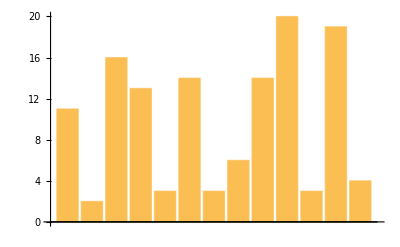
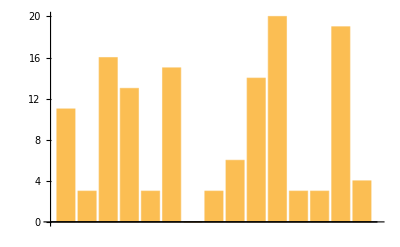
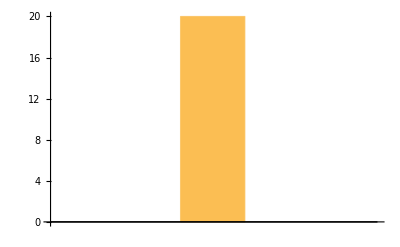
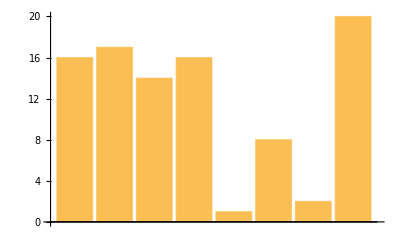
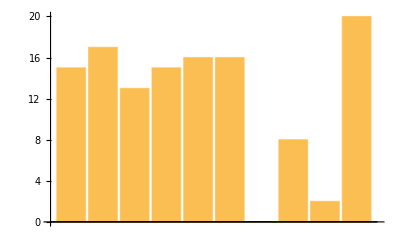
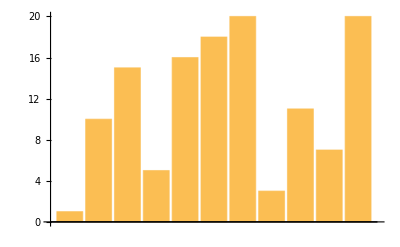
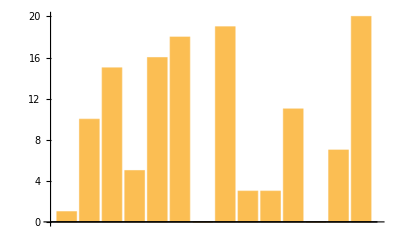
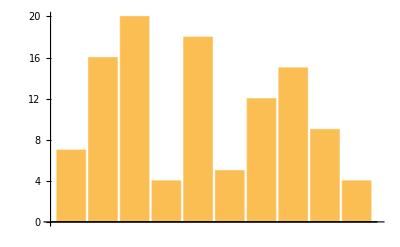
Input | Output | expected Output
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*defining a sample of the list data*)
samplelist=RandomSample[testinglist,10];
(*visually representing the output of the network reading the relative heights*)
Grid[Prepend[Map[
	{Show[Import[#[[1]]],ImageSize->200],BarChart[ocrNetTrained[#[[1]]]],BarChart[#[[2]]]}&,samplelist],
	{"Input", "Output", "expected Output"}],Frame->All]
```

For many of the bar charts, the network is doing fairly well. It is getting the general idea of the ups and downs and the number of bars. However, It has problems distinguishing between bars that are close together and of similar lengths as well as very low bars. The first error is likely due to the inability to know how many bars there are and going for a default of 1, the second error is due to the low loss associated with low bars.

## Combining the networks into a graph-reading function

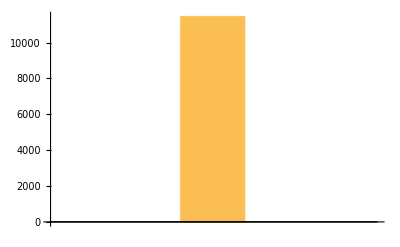
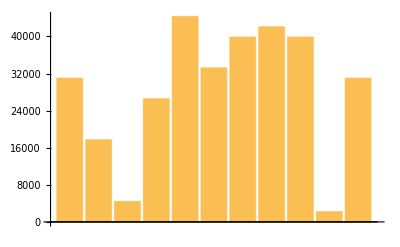
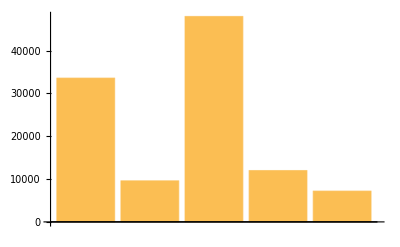
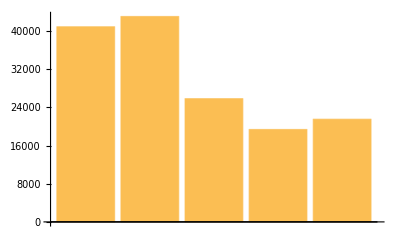
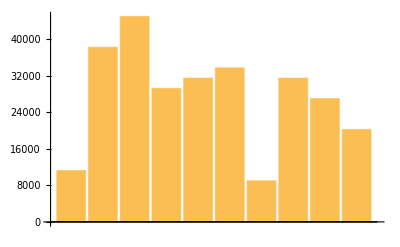
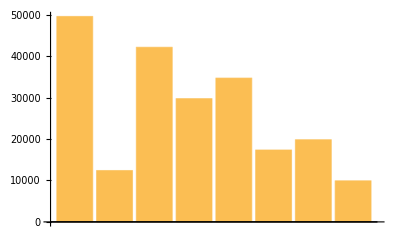
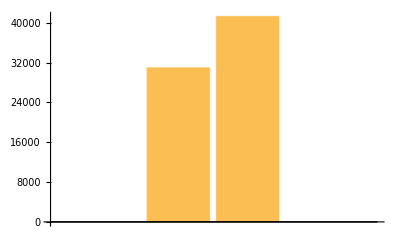
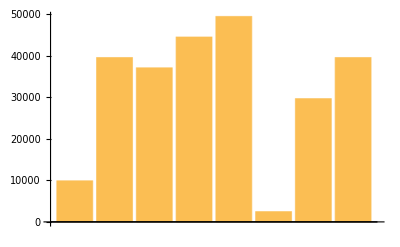
Input | Output
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
readGraph[graph_]:=Flatten[Map[#*(vgg16NetTrained[graph]/20)&,ocrNetTrained[graph]]]
SetAttributes[readGraph,Listable]
Grid[Prepend[Map[{Show[Import[#],ImageSize->200],BarChart[readGraph[#]]}&,sample[[All,1]]],
	{"Input", "Output"}],Frame->All]
```

We see that the network has gotten reasonably good at reading the bar charts given to it, however it is not doing so well on pictures of bar charts I looked up on the internet. For some of them it is getting a rough idea of whats going on, but none of the readings are useful. I have high hopes that this project can be expanded upon to reduce over-fitting for the specific type of graph. One important step is varying the image size which will introduce some variation in the labels.

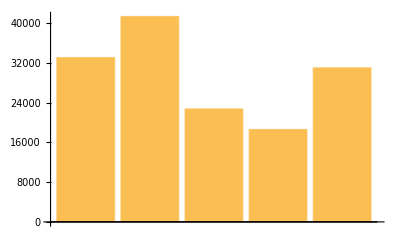
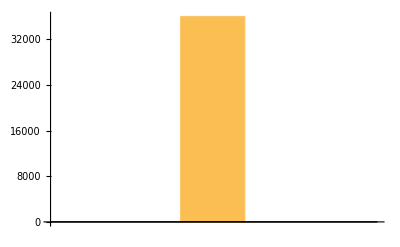
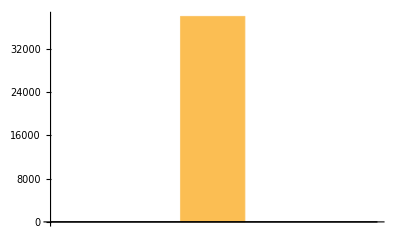
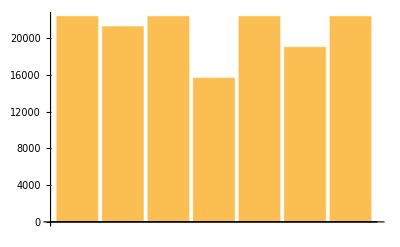
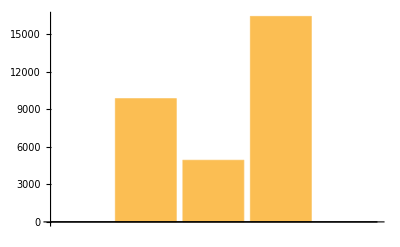
Chart | Interpretation
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Prepend[Map[{Show[#,ImageSize->200],BarChart[readGraph[#]]}&,],{"Chart","Interpretation"}],
	Frame->All]
```